#### Polar coordinate system

x = r cos(θ)
y = r sin(θ)

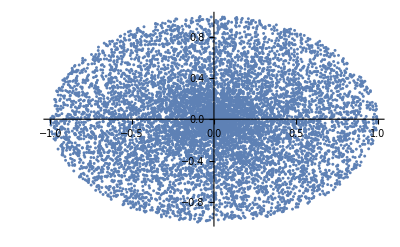

```mathematica
polarWrong=Module[{radius,r,θ,x,y,data},
radius=1;
data={};
For[i=0,i<10^4,i++,
r=RandomReal[]*radius;
θ=RandomReal[]*2Pi;
x=r*Cos[θ];
y=r*Sin[θ];
AppendTo[data,{x,y}]
];
data
];
ListPlot[polarWrong,PlotMarkers->{Automatic,3}]
```

In Cartesian coordinates an infinitesimal area element can be calculated as dA = dx dy. Using the Jacobian determinant one can convert the formula to other coordinate systems.

dA = dx dy = J dr dθ = r dr dθ,
where J = det(∂(x, y))/(∂(r, θ))

PDF for r
f(r) =  r/R, where R - radius

CDF for r
F(r) = (r/R)^2

Depends on r ⇒ Inverse transform sampling
let u = (r/R)^2 where u→Uniform(0, 1)
then r = u^(1/2)R

No dependence in PDF on θ ⇒ θ→Uniform(0, 2π)

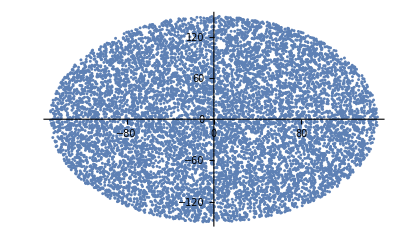

```mathematica
polarCorrect=Module[{radius,r,θ,x,y,data,u},
radius=150;
data={};
For[i=0,i<10^4,i++,
u=RandomReal[];
r=u^(1/2)*radius;
θ=RandomReal[]*2Pi;
x=r*Cos[θ];
y=r*Sin[θ];
AppendTo[data,{x,y}]
];
data
];
ListPlot[polarCorrect,PlotMarkers->{Automatic,3}]
```

#### Spherical coordinate system

x = r cos(θ) sin(ϕ)
y = r sin(θ) sin(ϕ)
z = r cos(ϕ)

```mathematica
sphericalWrong=Module[{radius,r,θ,ϕ,x,y,z,data},
radius=1;
data={};
For[i=0,i<10^4,i++,
r=RandomReal[]*radius;
θ=RandomReal[]*2Pi;
ϕ=RandomReal[]*Pi;
x=r*Cos[θ]*Sin[ϕ];
y=r*Sin[θ]*Sin[ϕ];
z=r*Cos[ϕ];
AppendTo[data,{x,y,z}]
];
data
];
ListPointPlot3D[sphericalWrong,PlotStyle->PointSize[Medium]]
```

-Graphics3D-

```mathematica
sphericalWrong2=Module[{radius,r,θ,ϕ,x,y,z,data,u},
radius=1;
data={};
For[i=0,i<10^4,i++,
u=RandomReal[];
r=u^(1/2)*radius;
θ=RandomReal[]*2Pi;
ϕ=RandomReal[]*Pi;
x=r*Cos[θ]*Sin[ϕ];
y=r*Sin[θ]*Sin[ϕ];
z=r*Cos[ϕ];
AppendTo[data,{x,y,z}]
];
data
];
ListPointPlot3D[sphericalWrong2,PlotStyle->PointSize[Medium]]
```

-Graphics3D-

In Cartesian coordinates an infinitesimal volume element can be calculated as dV = dx dy dz. Using the Jacobian determinant one can convert the formula to other coordinate systems.

dV = dx dy dz = J dr dθ dϕ = r^2sin(ϕ) dr dθ dϕ,
where J = det(∂(x, y, z))/(∂(r, θ, ϕ))

CDF for r
F(r) = (r/R)^3

Depends on r ⇒ Inverse transform sampling
let u = (r/R)^3 where u→Uniform(0, 1)
then r = u^(1/3)R

PDF for ϕ
f(ϕ) = 1/2 sin(ϕ)

CDF for ϕ
F(ϕ) = -1/2 cos(ϕ) + 1/2

Depends on ϕ ⇒ Inverse transform sampling
let v = -1/2 cos(ϕ) + 1/2 where v→Uniform(0, 1)
then ϕ = arccos(1-2v)

No dependence in PDF on θ ⇒ θ→Uniform(0, 2π)

```mathematica
sphericalCorrect=Module[{radius,r,θ,ϕ,x,y,z,data,u,v},
radius=1;
data={};
For[i=0,i<10^3,i++,
u=RandomReal[];
r=u^(1/3)*radius;
θ=RandomReal[]*2Pi;
v=RandomReal[];
ϕ=ArcCos[1-2v];
x=r*Cos[θ]*Sin[ϕ];
y=r*Sin[θ]*Sin[ϕ];
z=r*Cos[ϕ];
AppendTo[data,{x,y,z}]
];
data
];
ListPointPlot3D[sphericalCorrect,PlotStyle->PointSize[Medium]]
```

-Graphics3D-

#### The END